```mathematica
Clear[A,B]
A[x_,y_]:=1/2{0,0,1}×{x,y,0}
A[x_,y_]:=1/2{0,0,1 + Sin[x]}×{x,y,0}//FullSimplify
(*A[x_,y_]:=1/2{0,0,1- x }×{x,y,0}//FullSimplify*)
A[x,y]
Div[A[x,y],{x,y,z}]//FullSimplify
B[x_,y_]=Curl[A[x,y],{x,y,z}]//FullSimplify
```

{-1/2 y (1+Sin[x]),1/2 x (1+Sin[x]),0}

-1/2 y Cos[x]

{0,0,1+1/2 x Cos[x]+Sin[x]}

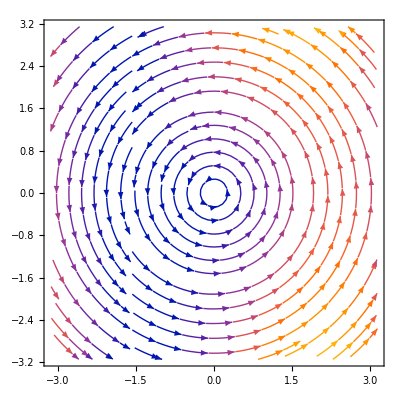

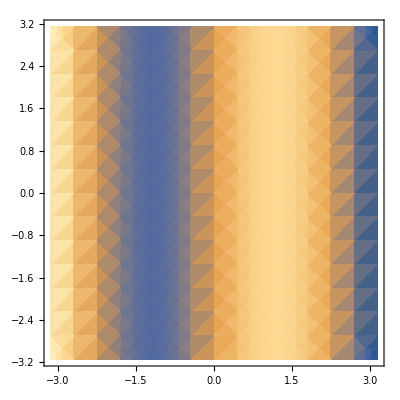

```mathematica
StreamPlot[A[x,y][[;;2]],{x,-π,π},{y,-π,π}]
DensityPlot[B[x,y][[3]],{x,-π,π},{y,-π,π},PlotRange->Full]
```

```mathematica
Div[A[x,y],{x,y,z}]
Curl[A[x,y],{x,y,z}]
```

-1/2 y Cos[x]

{0,0,1+1/2 x Cos[x]+Sin[x]}

```mathematica
bmr={x,y,z};
bmr0={x0,y0,z0};
bmr0=0*{x0,y0,z0};
```

```mathematica
Table[(D[A[x,y][[1]],{bmr[[i]],1}]/.(#[[1]]->#[[2]]&/@({bmr,bmr0}ᵀ))),{i,Length[bmr]}]//FullSimplify
Table[(D[A[x,y][[2]],{bmr[[i]],1}]/.(#[[1]]->#[[2]]&/@({bmr,bmr0}ᵀ))),{i,Length[bmr]}]//FullSimplify
```

{0,-1/2,0}

{1/2,0,0}

```mathematica
Table[{i,j,1/2(D[A[x,y][[1]],{bmr[[i]],1},{bmr[[j]],1}]/.(#[[1]]->#[[2]]&/@({bmr,bmr0}ᵀ)))},{i,Length[bmr]},{j,Length[bmr]}]//TableForm
Table[{i,j,1/2(D[A[x,y][[2]],{bmr[[i]],1},{bmr[[j]],1}]/.(#[[1]]->#[[2]]&/@({bmr,bmr0}ᵀ)))},{i,Length[bmr]},{j,Length[bmr]}]//TableForm
```

1
1
0 | 1
2
-1/4 | 1
3
0
2
1
-1/4 | 2
2
0 | 2
3
0
3
1
0 | 3
2
0 | 3
3
0

1
1
1/2 | 1
2
0 | 1
3
0
2
1
0 | 2
2
0 | 2
3
0
3
1
0 | 3
2
0 | 3
3
0